# Fully implicit scheme for square wave voltammetry

## - using expanding space grid

## - square wave on a staircase

Version 2.0
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
xTicks1[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/4//N}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/4//N}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/20//N}]];

yTicks2[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/4//N}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/4//N}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/20//N}]];

xTicks3[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/4}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/4}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/20}]];

yTicks4[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/4}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/4}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/20}]];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{ColorData["Legacy","NavyBlue"],AbsoluteThickness[.5]},FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
(*options for voltammograms*)
optionA={
(*PlotRange:>{{0,n},{Min[acv1]-0.1,Max[acv1]+0.1}},*)
FrameTicks-> {Automatic,yTicks2,Automatic,yTicks4},
PlotStyle->{Red,AbsoluteThickness[0.7]},
FrameLabel->{
Style["increment",FontFamily->"Arial" ,FontSize-> 12,FontColor->Black],
Style["χ",FontFamily-> "Times New Roman" ,FontSize->  12, FontWeight->  "Plain",FontColor->Black],
None,
None}
};
```

```mathematica
(*options for voltammograms*)
optionB={
PlotStyle-> {Red,AbsoluteThickness[0.7]},
FrameTicks:>  {xTicks1,yTicks2,xTicks3,yTicks4},
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontColor-> Black,FontSlant-> Italic,FontSize-> 12],
Style["χ",FontFamily-> "Times New Roman",FontSlant-> Italic,FontColor->Black,FontSize-> 12],
None,
None}
};
```

```mathematica
optionD={
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["χ",FontFamily-> "Times New Roman",FontSize-> 12, FontWeight-> "Plain"],
None,
None},
Epilog:>  {Text["χ_b",{0,Max[squareBack⟦All,2⟧]-.1}],Text["χ_f",{0,Min[squareFor⟦All,2⟧]+.1}],Text["Δχ",{0,Min[squareDiff⟦All,2⟧]+.1}]}};
```

```mathematica
(*options for power spectrum plots*)
optionMain={
PlotStyle->{Black,AbsoluteThickness[0.7]},
FrameTicks->Automatic,
FrameLabel->{"Frequency / π",None,None,None},
DisplayFunction->Identity};
```

```mathematica
(*options for power spectrum plots*)
optionInset={
PlotStyle->{Black,AbsoluteThickness[0.7]},
FrameTicks->Automatic,
PlotRange->{{(2*Ω/Pi)-2,(2*Ω/Pi)+2},{0,0.12}},
BaseStyle->{FontSize->7},
FrameLabel->{"Frequency / π",None,None,None},
DisplayFunction->Identity};
```

```mathematica
dcOptions={
Joined-> True,
PlotStyle->{Red,Thickness[0.003]},
FrameTicks-> Automatic,
FrameLabel-> {
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["√πχ",FontFamily-> "Times New Roman",FontSize-> 12, FontWeight-> "Plain"],
None,
None}
};
```

```mathematica
$Line=0;
```

## Make Diagonals

```mathematica
Clear[makeVarDiagonals];

makeVarDiagonals[m_Integer,d_][a_]:=
	Module[{x,y,z},
		x=Table[-d*a^(4-2*j),{j,3,m-1}];(*lower diagonal*)
		z=Table[-d*a^(3-2*j),{j,2,m-2}];(*upper diagonal*)
		y=Table[1+(1+a)*d*a^(3-2*j),{j,2,m-1}];(*centre*)
{x,y,z}]
```

```mathematica
Clear[𝔻,a,x,y,z];
{x,y,z}=makeVarDiagonals[7,𝔻][a]
Table[Switch[j-i,-1,x⟦j⟧,0,y⟦j⟧,1,z⟦j-1⟧,_,0],{i,4},{j,4}]//MatrixForm
```

{{-𝔻/a^2,-𝔻/a^4,-𝔻/a^6,-𝔻/a^8},{1+((1+a) 𝔻)/a,1+((1+a) 𝔻)/a^3,1+((1+a) 𝔻)/a^5,1+((1+a) 𝔻)/a^7,1+((1+a) 𝔻)/a^9},{-𝔻/a,-𝔻/a^3,-𝔻/a^5,-𝔻/a^7}}

(1+((1+a) 𝔻)/a | -𝔻/a | 0 | 0
-𝔻/a^2 | 1+((1+a) 𝔻)/a^3 | -𝔻/a^3 | 0
0 | -𝔻/a^4 | 1+((1+a) 𝔻)/a^5 | -𝔻/a^5
0 | 0 | -𝔻/a^6 | 1+((1+a) 𝔻)/a^7)

## Set Up Solution

```mathematica
Clear[implicitSolveExpStaircaseSW];

implicitSolveExpStaircaseSW[m_Integer,n_Integer,d_,{lowerLimit_,upperLimit_},{ksStar_,α_},{Δ𝔼s_,Δ𝔼sw_,tN_},a_]:=Module[{x,y,z,len,mat,y1,z1,initial,range,τ,solveNext},

range=(upperLimit+Abs[lowerLimit]);
τ=range/n;

{x,y,z}=makeVarDiagonals[m,d][a];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
y1=y⟦1⟧;
z1=z⟦1⟧;
initial=ConstantArray[1.,{m}];

solveNext[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2,tmp3},

ξ=Exp[upperLimit-(Δ𝔼s*((k-Mod[k,2*tN])/(2*tN)))-(Δ𝔼sw*2.*(-0.5+UnitStep[-Mod[k,2*tN]+(tN-1)]))];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));

b=list[[2;;-2]];
b⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));
b⟦-1⟧+=d*a^(5-2*m);
mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;
tmp2=LinearSolve[mat,b];
tmp3=Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]
];

Rest@FoldList[solveNext,initial,Range[0,n]]
]
```

## Set Parameter Values

### Variables/ constants

```mathematica
Clear[F,R,T,f,𝒟];

F=N@QuantityMagnitude[UnitConvert@Quantity["FaradayConstant"]];(*Faradays constant*)

R=N@QuantityMagnitude[UnitConvert@Quantity["GasConstant"]];(*gas constant*)

T=298.15;(*temperature*)
f=F/(R*T);
𝒟=1.*^-5;(*diffusion coefficient*)
```

### Electrochemical variables

```mathematica
Clear[α,ks,tp,Δ𝔼s,Δ𝔼sw,upperLimit,range];
α=0.5;

ks=1.*^3;(*standard rate constant*)

tp=0.1;(*period in seconds*)

Δ𝔼s=f*0.005;(*dimensionless staircase step size = f × amplitude in V*)

Δ𝔼sw=f*0.05;(*dimensionless square wave step size = f × amplitude in V*)

upperLimit=10.;(*initial potential versus the formal potential*)

range=20.;(*approximate range required*)
```

### Simulation variables

```mathematica
Clear[𝔻,cycles,lowerLimit,tN,n,a,temp,m,τ,time,υ,ksStar,Ω,ω,conc,y1,z1,c];

𝔻=2.;

cycles=Round[range/Δ𝔼s];

range=cycles*Δ𝔼s;

lowerLimit=upperLimit-range;(*limit = f×(E-E^o)*)

tN=50;(*number of increments per half square wave cycle*)

n=cycles*2*tN;

a=1.1;
temp=Solve[∑_(j=1)^(mm-1) a^(j-1)==6*√((𝔻*(1+a)*(n-1))/2),mm,InverseFunctions-> True];

m=Ceiling[mm/.temp⟦1⟧];(*number of spacial grid points*)

τ=range/n; (*calculation of the incremental time/potential step*)

time=cycles*tp;

υ=range/(f*time);(*notional sweep rate*)

ksStar=2.ks*Sqrt[time/(𝒟*𝔻*(n-1))];(*dimensionless rate constant*)

Ω=2*Pi*cycles/range;(*calculation of the dimensionless angular frequency*)

ω=2*Pi/tp;(*calculation of the dimensional angular frequency*)
```

## Show waveform

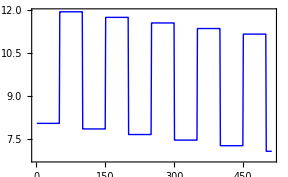

```mathematica
staircase=Table[upperLimit-(Δ𝔼s*((k-Mod[k,2*tN])/(2*tN)))-(Δ𝔼sw*2.*(-0.5+UnitStep[-Mod[k,2*tN]+(tN-1)])),{k,0,2^9}];

ListPlot[staircase]
```

## Solve

```mathematica
c=implicitSolveExpStaircaseSW[m,n,𝔻,{lowerLimit,upperLimit},{ksStar,α},{Δ𝔼s,Δ𝔼sw,tN},a];//Timing
```

{1.92189,Null}

## Plot square wave voltammogram

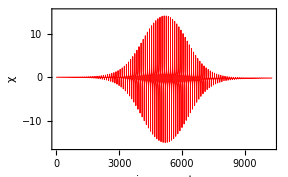

```mathematica
swv1=Map[(((2.+a)*a*#⟦1⟧-((1.+a)^2*#⟦2⟧)+#⟦3⟧)*√((𝔻*(n-1))/(2.*a^2*(1.+a)*range)))&,c];
plot1=ListPlot[swv1,optionA,PlotRange-> {{0,n},{Min[swv1]-1,Max[swv1]+1}}]
```

```mathematica
convert[i_,{j_}]:={upperLimit-(τ*j),i}
```

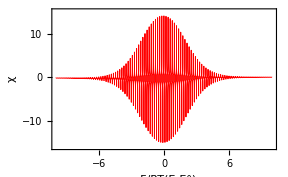

```mathematica
swv2=MapIndexed[convert,swv1];

plot2=ListPlot[swv2,optionB,PlotRange-> {{-10,10},{Min[swv1]-1,Max[swv1]+1}}]
```

## "Traditional" plot

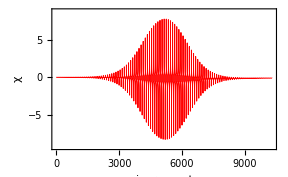

```mathematica
swv4=Map[(((2.+a)*a*#⟦1⟧-((1+a)^2*#⟦2⟧)+#⟦3⟧)*√((𝔻*Pi*(n-1))/(2.*a^2*(1.+a)*cycles*2.)))&,c];
plot1=ListPlot[swv4,optionA,PlotRange-> {{0,n},{Min[swv4]-1,Max[swv4]+1}}]
```

Check that the switching from +ve to -ve is correct.

```mathematica
Length/@Split[Table[Sign[swv4⟦i⟧],{i,1,15*tN+2}]]
```

{50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,2}

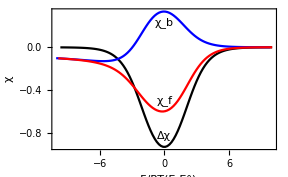

```mathematica
Block[{$DisplayFunction=Identity},

(*forward current*)
squareFor=Table[{upperLimit-(Δ𝔼s*((k-Mod[k,2*tN])/(2*tN))),swv4⟦k⟧},{k,tN,Length[swv4],2*tN}];
squareForPlot=ListPlot[squareFor,PlotStyle-> {Red}];

(*backward current*)
squareBack=Table[{upperLimit-(Δ𝔼s*((k-Mod[k,2*tN])/(2*tN))),swv4⟦k⟧},{k,2*tN,Length[swv4],2*tN}];
squareBackPlot=ListPlot[squareBack,PlotStyle-> {Blue}];

(*difference current*)
squareDiff=Table[{squareFor⟦j,1⟧,(squareFor⟦j,2⟧-squareBack⟦j,2⟧)},{j,1,Length[squareBack]-1}];
squarePlot=ListPlot[squareDiff,PlotStyle-> {Black}];]

Show[squarePlot,squareBackPlot,squareForPlot,PlotRange->All,optionD]
```

Find the peak from the data:

```mathematica
peakHeight=Min[squareDiff⟦All,2⟧];
Select[squareDiff,#⟦2⟧==peakHeight&]//Flatten;
Print["peak at ",%⟦1⟧*1000/f," mV with height ",peakHeight]
```

peak at 1.92579 mV with height -0.92943

Find the peak by interpolation:

```mathematica
int=Interpolation[squareDiff];
Quiet[res=FindMinimum[int[xx],{xx,0}]];
Print["peak at ",res⟦2,1,2⟧*1000/f," mV with height ",res⟦1⟧]
```

peak at -0.259742 mV with height -0.930145

## Moving average filter

Filter data with a moving average filter to remove ac component then re-plot data. If necessary repeat the filtering a second time.

```mathematica
?MovingAverage
```

The moving average filter averages over N points with N being the number of increments per cycle.

```mathematica
data2=MovingAverage[swv1,2*tN];
data2=MovingAverage[data2,2*tN];
```

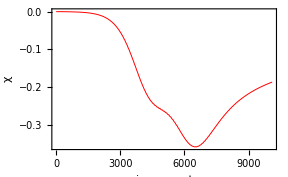

```mathematica
plot3=ListPlot[data2, optionA]
```

The moving average chops the data list. To subtract the unfiltered data, swv1, from the filtered data, data2, we need to align the lists. We do this by first determining the length of the over hang.

```mathematica
Clear[xx];
xx=Length[swv1]-Length[data2]
```

198

```mathematica
convert2[i_,{j_}]:={upperLimit-(xx*τ/2.)-(τ*j),i}
```

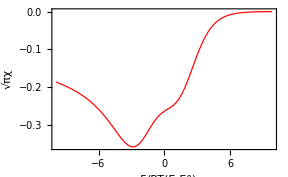

```mathematica
swv3=MapIndexed[convert2,data2];

plot2=ListPlot[swv3,dcOptions]
```

The peak height and peak position are now obtained. Better accuracy is obtained by increasing the magnitude of n.

```mathematica
peakHeight=Min[swv3⟦All,2⟧];
Select[swv3,#⟦2⟧==peakHeight&]//Flatten;
Print["peak at ",%⟦1⟧*1000/f," mV with height ",peakHeight]
```

peak at -75.7742 mV with height -0.35889

## Fourier transform filter

```mathematica
powerSpectrum[a_,{b_}]:={(b-1)*Ω/(cycles*Pi),a}
```

```mathematica
fourierData=Abs[Fourier[swv1]];
fourierData=MapIndexed[powerSpectrum,fourierData];
peak=Select[fourierData,(#⟦1⟧==Ω/π)&];
```

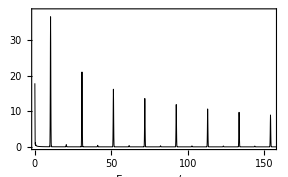

```mathematica
pRange={PlotRange:> {{1,Ceiling[15*Ω/π]},{0,Ceiling[peak⟦1,2⟧]+1}}};

mainPlot=ListPlot[fourierData,optionMain,pRange]
```

```mathematica
fourierFilter[list_List,x_Integer,y_Integer]:=Module[{a,b},
a=Fourier[list];b=Join[Table[0,{j,1,x-1}],Table[a⟦j⟧,{j,x,y}],Table[0,{j,1,Length[a]-(2*(y+1))}],Table[a⟦j⟧,{j,Length[a]-(y+1),Length[a]-(x-1)}],Table[0,{j,1,x-1}]];Re[InverseFourier[b]]];
```

Convert from dimensionless linear sweep to dimensionless ac by multiplying by 1/(Δ E)√(υ/ω)

#### 1st component

```mathematica
newdata=fourierFilter[swv1,(cycles+1)-12,(cycles+1)+12]*Sqrt[Abs[f*υ]/ω]/Δ𝔼sw;

(*add dimensionless potential scale to the x axis*)

firstComponent=MapThread[{#1⟦1⟧,#2}&,{swv2,newdata}];
```

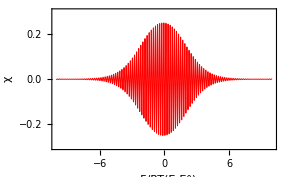

```mathematica
firstComponentPlot=ListPlot[firstComponent,optionB,PlotRange->{{lowerLimit,upperLimit},{Min[newdata]-0.05,Max[newdata]+0.05}}]
```

#### 2nd component

```mathematica
newdata2=fourierFilter[swv1,((3*cycles)+1)-11,((3*cycles)+1)+11]*Sqrt[Abs[f*υ]/ω]/Δ𝔼sw;

(*add dimensionless potential scale to the x axis*)

secondComponent=MapThread[{#1⟦1⟧,#2}&,{swv2,newdata2}];
```

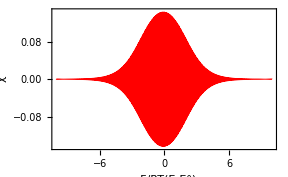

```mathematica
secondComponentPlot=ListPlot[secondComponent,optionB,PlotRange->{{lowerLimit,upperLimit},{Min[newdata2]-0.001,Max[newdata2]+0.001}}]
```

#### 3rd component

```mathematica
newdata3=fourierFilter[swv1,((5*cycles)+1)-11,((5*cycles)+1)+11]*Sqrt[Abs[f*υ]/ω]/Δ𝔼sw;

(*add dimensionless potential scale to the x axis*)

thirdComponent=MapThread[{#1⟦1⟧,#2}&,{swv2,newdata3}];
```

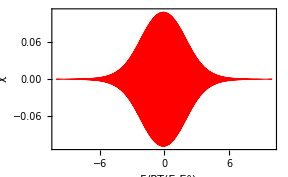

```mathematica
thirdComponentPlot=ListPlot[thirdComponent,optionB,PlotRange->{{lowerLimit,upperLimit},{Min[newdata3]-0.001,Max[newdata3]+0.001}}]
```

#### DC component

```mathematica
newdata4=fourierFilter[swv1,1,35];

(*add dimensionless potential scale to the x axis*)

dcComponent=MapThread[{#1⟦1⟧,#2}&,{swv2,newdata4}];
```

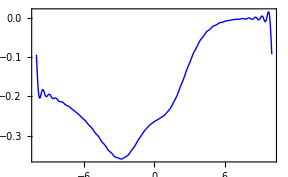

```mathematica
dcComponentPlot=ListPlot[dcComponent]
```